## DEFINE PARAMETERS

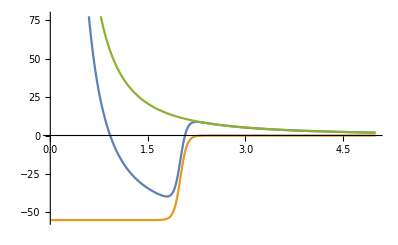

```mathematica
Subscript[m, N]=940;ℏc=197.327;
V0=55;R=2;a=0.05;μ=8/9 Subscript[m, N];l=1;
rmax=5.;dr=0.01;
rlist=Range[dr,rmax,dr];
len=Length[rlist];
Vwoods[r_]:=-V0/(1+Exp[(r-R)/a]);
Vcent[r_]:=(l(l+1)ℏc^2)/(2μ r^2);1
V[r_]:=-V0/(1+Exp[(r-R)/a])+(l(l+1)ℏc^2)/(2μ r^2);
Vmat=DiagonalMatrix[V[rlist]];
ListLinePlot[{V[rlist],Vwoods[rlist],Vcent[rlist]},DataRange->{dr,rmax}]
```

```mathematica
(*INITIAL HAMILTONIAN*)
one[n_,d_]:=
DiagonalMatrix[1+0Range[n-Abs[d]],d];
H0:=Vmat+-ℏc^2/(2 μ) 1/dr^2(one[len,-1]-2 one[len,0]+one[len,1]);
```

## SCATTERING SOLUTIONS

```mathematica
(*SCATTERING SOLUTION*)
k[En_?NumericQ]:=Sqrt[(2μ En)/ℏc^2];
wavescat[En_,r_,δ_,l_]:=1/2 Exp[I δ](Cos[δ]SphericalBesselJ[l,k[En] r]-Sin[δ] SphericalBesselY[l,k[En] r]);
(*Bscat[En_?NumericQ,δ_?NumericQ,l_]:=k[En] rmax(((Cos[δ] ∂_x SphericalBesselJ[l,x]/.x->k[En] rmax)-(Sin[δ] ∂_x SphericalBesselY[l,x]/.x->k[En] rmax))/(Cos[δ]SphericalBesselJ[l,k[En] rmax]-Sin[δ]SphericalBesselY[l,k[En] rmax]));*)
Bscat[En_?NumericQ,δ_?NumericQ,l_]:=rmax/wavescat[En,rmax,δ,l] D[wavescat[En,r,δ,l],r]/.{r->rmax};
(*HAMILTONIAN*)
Hnewscat[En_?NumericQ,δ_?NumericQ,l_]:=(H=H0;H[[len,len]]=Vmat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr Bscat[En,δ,l]/rmax-1);H);
(*RETURNS EIGEINVALUE*)
eigenvscat[En_?NumericQ,i_,δ_?NumericQ,l_]:=({eval,evec}=Transpose@SortBy[Transpose[Eigensystem[Hnewscat[En,δ,l]]],First];eval[[i]]);
(*FINDS ENERGY LEVEL AND PHASE*)
(*findnd[En_]:=Module[{phase=List[],n=1},(While[Max[Table[eigenvscat[{En,n,δ,l}][[1]],{δ,0.,π,0.01}]]<En,n++;];phase=Table[{eigenvscat[{En,n,δ,l}][[1]],δ},{δ,0,π,0.001}];δ=phase[[Position[phase[[All,1]],Nearest[phase[[All,1]],En][[1]]][[1,1]],2]];{n,δ})]*)
findnd[En_?NumericQ]:=Module[{n=1},While[Max[Table[eigenvscat[En,n,x,l],{x,0.,π,0.1}]]<En,n++;];δ=x/.FindRoot[eigenvscat[En,n,x,l]==En,{x,0.,-Pi,Pi}];If[δ<0,δ=π+δ];{n,δ}];
(*MATCHES AMPLITUDE AND PLOTS*)
constscat[i_]:=evec[[i,-1]]/wavescat[eval[[i]],rmax,δ,l];
wvplot[En_]:=Module[{n=findnd[En][[1]],δ=findnd[En][[2]]},{eval,evec}=Transpose@SortBy[Transpose[Eigensystem[Hnewscat[En,δ,l]]],First];Print[{En,eval[[n]],n,δ}];ListLinePlot[{Transpose[{rlist,evec⟦n⟧}],Transpose[{Range[rmax,rmaxx,dr],Re[constscat[n] wavescat[eval[[n]],Range[rmax,rmaxx,dr],δ,l]]}]},PlotRange->All]]
```

{1.30748,1.30748+0. ⅈ,1,1.22782+0. ⅈ}

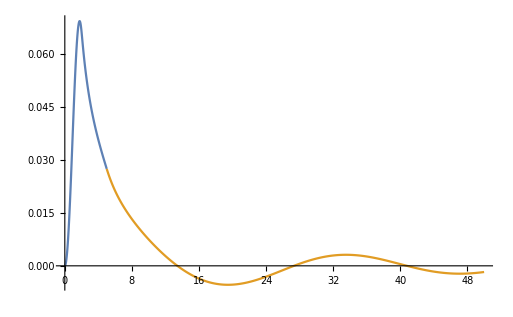
{15.9567,-Graphics-}

```mathematica
rmaxx=50.;
wvplot[1.30748]//Timing
```

```mathematica
phasedata=Table[{x,findnd[x][[2]]},{x,0.5,2.0,0.01}];
```

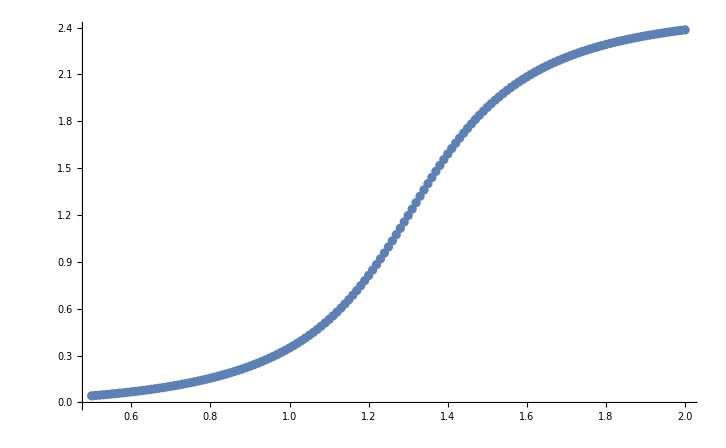

```mathematica
ListPlot[phasedata,DataRange->{0.5,2.0},GridLines->{None, {{Pi/2,Red}}}]
```

```mathematica
findres[n_]:=(phase[y_?NumericQ]:=Re[FindRoot[eigenvscat[y,n,x,l]==y,{x,0.,-Pi,Pi}][[1,2]]];Subscript[δ, res]=y/.FindRoot[phase[y]==Pi/2,{y,1.3,1,1.6}])
```

```mathematica
Subscript[δ, res]=findres[1]
```

1.39441

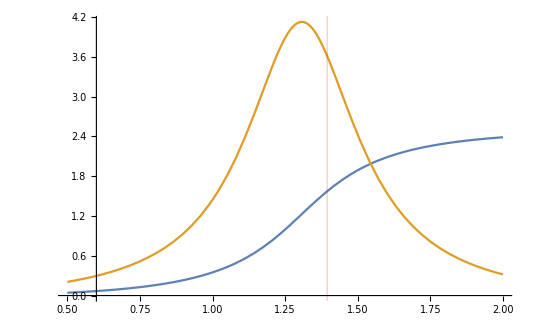

```mathematica
funcphasedata=Interpolation[phasedata,Method->"Spline"];
dfuncphasedata=funcphasedata';
Plot[Evaluate[{funcphasedata[x],dfuncphasedata[x]}],{x,0.5,2.0},GridLines->{{{Subscript[δ, res],Red}},None}]
```

```mathematica
1/(D[funcphasedata[x],x]/.x->findres[1])
```

0.27667

## RESONANCE STATES

```mathematica
(*RESONANCE SOLUTION*)
k[En_?NumericQ]:=Sqrt[(2μ En)/ℏc^2];
waveres[En_?NumericQ,r_,l_]:=SphericalHankelH1[l,k[En] r];
Bres[En_?NumericQ,l_]:=rmax/waveres[En,rmax,l](D[waveres[En,r,l],r]/.r->rmax);
(*HAMILTONIAN*)
Hnewres[En_?NumericQ,l_]:=(H=H0;H[[len,len]]=Vmat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr Bres[En,l]/rmax-1);H);
(*RETURNS EIGENVALUE*)
eigenvres[{En_?NumericQ,i_,l_}]:=({eval,evec}=Transpose@SortBy[Transpose[Eigensystem[Hnewres[En,l]]],First];{eval[[i]],i,l})
(*eigenvres1[En_?NumericQ,i_,l_]:=({eval,evec}=Transpose@SortBy[Transpose[Eigensystem[Hnewres[En,l]]],First];eval[[i]])*)
```

```mathematica
ϵ=10^-10;
n=1;
evals=List[];evecs=List[];
```

```mathematica
(*RETURNS EIGENSYSTEM*)
(*En=x/.FindRoot[Im[eigenvres1[x,n,l]]==Im[x],{x,0.1+0.I,0.,V0}]//Timing*)
En=NestWhileList[eigenvres,{0,n,l},Abs[Abs[#1[[1]]]-Abs[#2[[1]]]]>ϵ&,2,10][[-1,1]];
evals=Append[evals,En];
evecs=Append[evecs,evec[[n]]];
```

```mathematica
(*MATCHES AMPLITUDE & PLOTS*)
constres[i_]:=Abs[evecs[[i,-1]]]/Abs[waveres[evals[[i]],rmax,l]];
rmaxx=10.;
Manipulate[ListLinePlot[{Transpose[{rlist,Abs[evecs⟦i⟧]}],Transpose[{Range[rmax,rmaxx,dr],constres[i]Abs[waveres[evals[[i]],Range[rmax,rmaxx,dr],l]]}]},PlotRange->All],{i,1,Length[evals],1}]
```

```mathematica
evals
```

{1.30748-0.235312 ⅈ}

## BOUND SOLUTIONS (l=0)

```mathematica
(*BOUND SOLUTION*)
κ[En_]:=Sqrt[(2μ Abs[En])/ℏc^2];
wavebound[En_,r_,l_]:=SphericalHankelH1[l,I κ[En] r];
Bbound[En_,l_]:=rmax/wavebound[En,rmax,l](D[wavebound[En,r,l],r]/.r->rmax);
(*HAMILTONIAN*)
Hnewbound[En_,l_]:=(H=H0;H[[len,len]]=Vmat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr Bbound[En,l]/rmax-1);H);
(*RETURNS EIGENVALUE*)
eigenvbound[{En_,i_,l_}]:=({eval,evec}=Transpose@SortBy[Transpose[Eigensystem[Hnewbound[En,l]]],First];{eval[[i]],i,l})
```

```mathematica
ϵ=10^-10;
n=1;
evals=List[];evecs=List[];
```

```mathematica
(*RETURNS EIGENSYSTEM*)
En=NestWhileList[eigenvbound,{-V0/2,n,l},Abs[#1[[1]]-#2[[1]]]>ϵ&,2,10][[-1,1]];
While[Re[En]<0,
evals=Append[evals,En];
evecs=Append[evecs,evec[[n]]];n++;En=NestWhileList[eigenvbound,{-V0/2,n,l},Abs[#1[[1]]-#2[[1]]]>ϵ&,2,10][[-1,1]];]
```

```mathematica
(*MATCHES AMPLITUDE & PLOTS*)
constbound[i_]:=evecs[[i,-1]]/Abs[wavebound[evals[[i]],rmax,l]];
rmaxx=10.;
Manipulate[ListLinePlot[{Transpose[{rlist,evecs⟦i⟧}],Transpose[{Range[rmax,rmaxx,dr],constbound[i]Abs[wavebound[evals[[i]],Range[rmax,rmaxx,dr],l]]}]},PlotRange->All],{i,1,Length[evals],1}]
```

Part::partw: Part 1 of {} does not exist.

Transpose::nmtx: The first two levels of {{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,«7»,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,«450»},«1»} cannot be transposed.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListLinePlot::lpn: {Transpose[{{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,«10»,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,«450»},«1»}],{«1»}} is not a list of numbers or pairs of numbers.